```mathematica
(*This file simulates how the CES model with Lab-equipment specification of p_K responds to the change of trade costs.*)
v[x_]=x^(1-σ); 
ϵ[x_]=-(x v''[x])/v'[x];
Subscript[ϵ, D]=ϵ[Subscript[ξ, D]];
Subscript[ϵ, X]=ϵ[Subscript[ξ, X]];
parameters={κ-> 7 ,ρ->0.8,w->1,L->50,δ->0.25,ψ->1,b->2,γ->1, σ-> 3.3};
eqn1=Subscript[ξ, D] (1-1/Subscript[ϵ, D])τ-Subscript[ξ, X](1-1/Subscript[ϵ, X])==0;
eqn2=1/(ε̃)-(1-ω̃)1/Subscript[ϵ, D]-ω̃ 1/Subscript[ϵ, X]==0;
eqn3=g+δ-(w L)/(κ Subscript[p, K])(1-(v'[Subscript[ξ, D]]+τ v'[Subscript[ξ, X]])/(Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]]))==0;
eqn4=g-(w L)/(κ Subscript[p, K] ε̃)+(ρ(ε̃-1))/(ε̃)+δ==0;
eqn5= ω̃-(Subscript[ξ, X] v'[Subscript[ξ, X]])/(Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]])==0;
eqn6= e Subscript[ξ, X](1-1/Subscript[ϵ, X])-τ w==0;
eqn7 =Le (Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]])-L(v'[Subscript[ξ, D]]+τ v'[Subscript[ξ, X]])==0; 
eqn8 = Subscript[p, K]-(ω̃ Subscript[ξ, X]+(1-ω̃) Subscript[ξ, D])==0;
neweqn1L=eqn1/.parameters;
neweqn2L=eqn2/.parameters;
neweqn3L=eqn3/.parameters;
neweqn4L=eqn4/.parameters;
neweqn5L=eqn5/.parameters;
neweqn6L=eqn6/.parameters;
neweqn7L=eqn7/.parameters;
neweqn8L=eqn8/.parameters;
Nvalue=Exp[g] /.parameters;(*we normalize N0=1, and consider t=1 *)
muvalue=Exp[g] (Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]] );(*we normalize N0=1, and consider t=1 *)
```

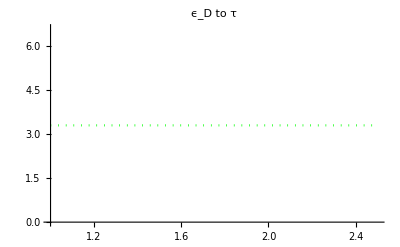

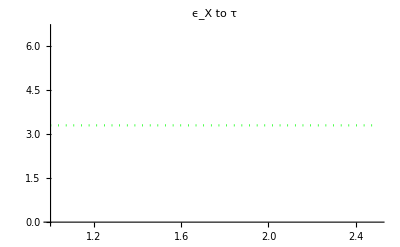

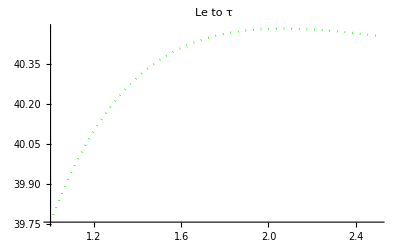

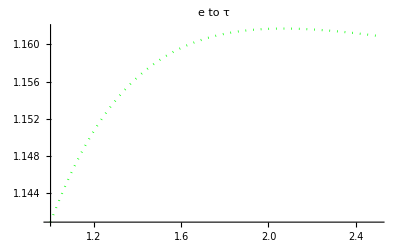

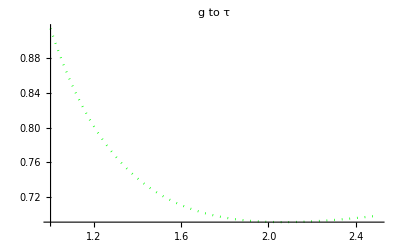

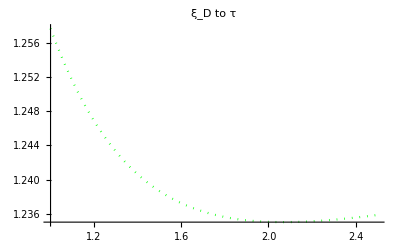

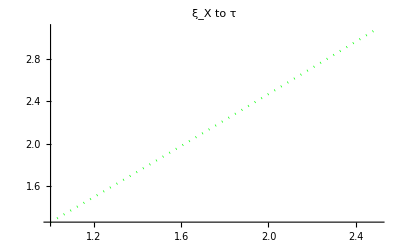

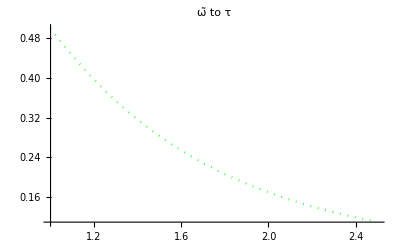

-Graphics-

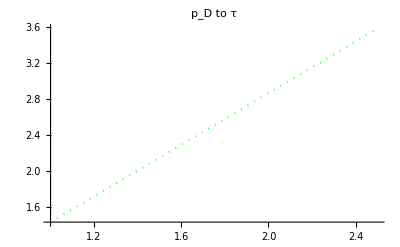

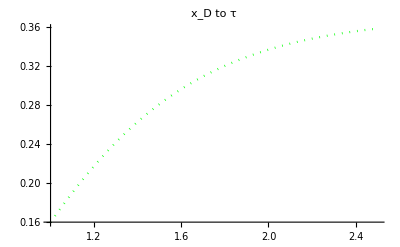

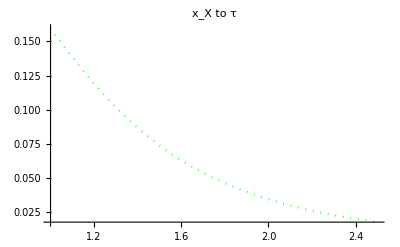

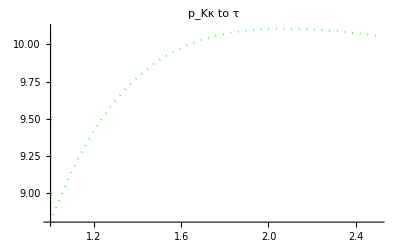

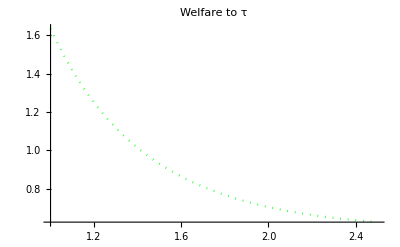

```mathematica
CEStauLE1=Plot[Subscript[ϵ, D]/.parameters/.
FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "ϵ_D to τ"]
CEStauLE2=Plot[Subscript[ϵ, X]/.parameters/.
FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "ϵ_X to τ"]
CEStauLE3=Plot[Le/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "Le to τ"]
CEStauLE4=Plot[e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "e to τ"]
CEStauLE5=Plot[g/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "g to τ"]
CEStauLE6=Plot[Subscript[ξ, D]/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "ξ_D to τ"]
CEStauLE7=Plot[Subscript[ξ, X]/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "ξ_X to τ"]
CEStauLE8=Plot[ω̃/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "ω̃ to τ"]
CEStauLE9=Plot[ε̃/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "ε̃ to τ"]
CEStauLE10=Plot[Subscript[ξ, D] e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "p_D to τ"]
CEStauLE11=Plot[Subscript[ξ, X] e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "p_D to τ"]
CEStauLE12=Plot[v'[Subscript[ξ, D]]/muvalue/.parameters/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "x_D to τ"]
CEStauLE13=Plot[v'[Subscript[ξ, X]]/muvalue/.parameters/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "x_X to τ"]
CEStauLE14=Plot[(ω̃ Subscript[ξ, X]+Subscript[ξ, D](1-ω̃))κ/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "p_Kκ to τ"]
CEStauLE15=Plot[1/ρ(Log[v[Subscript[ξ, D]]+v[Subscript[ξ, X]]]+ g/ρ)/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L,neweqn8L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20},{ Subscript[p, K],0.7}}],{τ,1,2.5},PlotStyle-> {Green,Dotted},PlotLabel-> "Welfare to τ"]
```

```mathematica
allCEStauLE={{CEStauLE1,CEStauLE2,CEStauLE3,CEStauLE4},{CEStauLE5,CEStauLE6,CEStauLE7,CEStauLE8},{CEStauLE9,CEStauLE10,CEStauLE11,CEStauLE12},{CEStauLE13,CEStauLE14,CEStauLE15}}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}